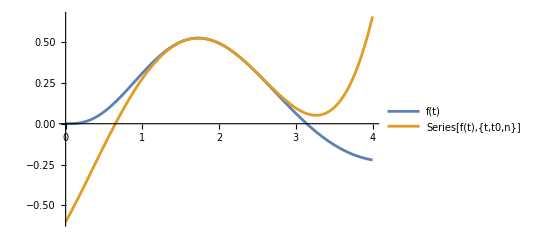

```mathematica
(*Funkcija iz DN*)
f[t_]:=Sin[t] t^2 Exp[-t]

(*Rzširitev okoli točke t0 = 2*)
t0=2;

(*Red Taylorjeve vrste*)
n=4;

(*Razvoj vrste*)
taylorSeries=Normal[Series[f[t],{t,t0,n}]];

(*Izris funkcije*)
Plot[{f[t],taylorSeries},{t,0,4},PlotLegends->{"f(t)",HoldForm[Series[f[t],{t,t0,n}]]/. HoldPattern[Power[t-t0,k_]]:>(t-t0)^k}]


Manipulate[Module[{approximation},approximation=Normal[Series[f[t],{t,t0,order}]];
Plot[{f[t],approximation},{t,0,4},PlotLegends->{"f(t)",HoldForm[Series[f[t],{t,t0,order}]]/. HoldPattern[Power[t-t0,k_]]:>(t-t0)^k},PlotLabel->Row[{"Order ",order," approximation around t =",t0}]]],{{order,1,"Order:"},1,10,1}]
```